# Assignment 08:

## On Response of Linear systems to arbitrary inputs

#### Aarya G (EP23B025) Engineering Physics

Date: 18th Oct 2023

## Introduction

Circuits are often used to transmit signals. In this assignment we look at Output signal of various input signals in RC and RLC Circuits. NDSolve gives us ability to analyse piecewise inputs without having to compute them by hand.

## RC circuit

### Step input

Input

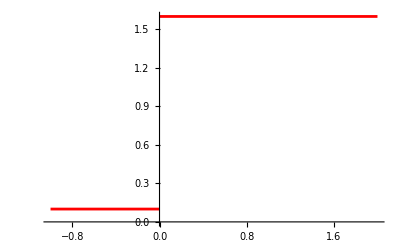

{{v→InterpolatingFunction[…]}}

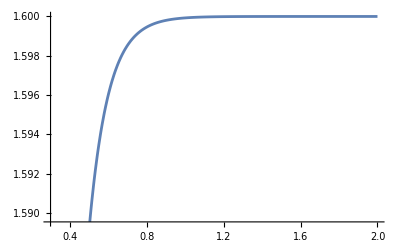

```mathematica
Clear["Global`*"]
Vin[t_]:=1.5 HeavisideTheta[2 t]+0.1
Print["Input"]
pltin = Plot[Vin[t],{t,-1,2}, PlotStyle->Red]
r = 100;
c = 10^(-3);
τ = r *c;
eqn = v'[t] * τ + v[t]==Vin[t];
Vo = NDSolve[{eqn,v[0.001]==0},v,{t,0,2 }]
plto = Plot[Evaluate[v[t] /. Vo],{t,0.3,2}]
```

### Piecewise input

Piecewise[{{(-1+t)^2, 0<t<1}, {Log[t], t≥1}, {0, True}}]

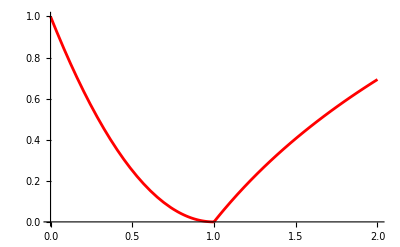

{{v→InterpolatingFunction[…]}}

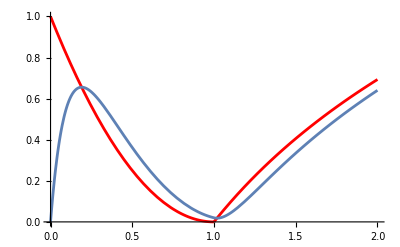

```mathematica
Clear["Global`*"]
Vin[t_] = Piecewise[{{(t-1)^2,0<t<1  } , {Log[t],t>=1}}]
pltin = Plot[Vin[t],{t,0,2}, PlotStyle->Red]
eqn = v'[t] * 0.1 + v[t]==Vin[t]; /. τ -> 0.1
Vo = NDSolve[{eqn,v[0]==0},v,{t,0,2,0.1 }]
plto = Plot[Evaluate[v[t] /. Vo],{t,0,2}];
Show[{pltin,plto}]
```

### Square Pulse

Piecewise[{{0.6 SquareWave[t], t<0.003}, {0, True}}]

{{v→InterpolatingFunction[…]}}

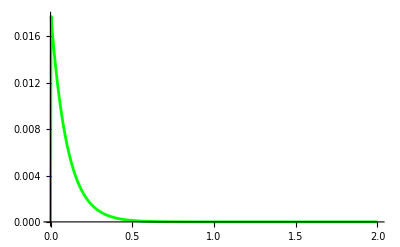

```mathematica
Clear["Global`*"]
Vin[t_] = Piecewise[{{0.6 *SquareWave[t], t<0.003}, {0, t>0.003}}]
eqn = v'[t] * 0.1 + v[t]==Vin[t]; 
Vo = NDSolve[{eqn,v[0]==0},v,{t,0,2,0.001 }]
Plot[Evaluate[v[t] /. Vo],{t,0,2}, PlotRange->All, PlotStyle->Green]
```

#### Transfer Function

1/(1+(ⅈ ω)/10)

1/(1+ω^2/100)

-ω/(10 (1+ω^2/100))

ArcTan[ω/10]

√(1/((1+ω^2/100)^2)+ω^2/(100 (1+ω^2/100)^2))

Real Part

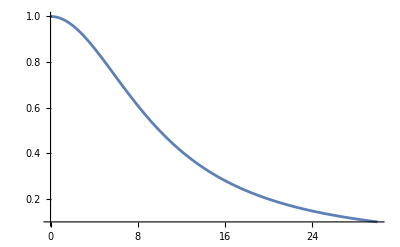

Imaginary part

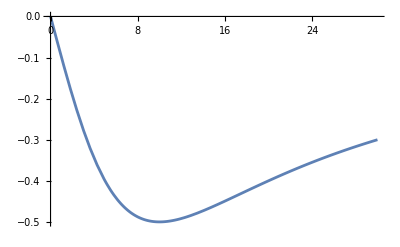

Phase

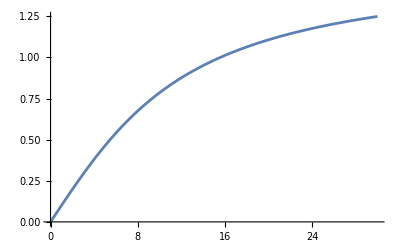

Absolute value

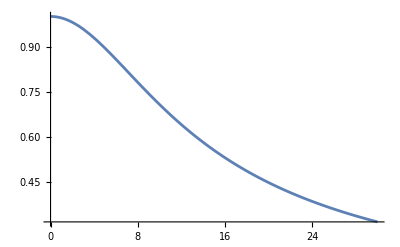

```mathematica
r = 100;
c = 10^(-3);
H[ω_] = 1/(1+ I ω r c)
RealH[ω_] = 1/(1+(ω r c )^2)
ImH[ω_] =- ω r c /(1+(ω r c )^2)
phase[ω_] =  -ArcTan[ ImH[ω]/RealH[ω]]
Len[ω_] = Sqrt[ImH[ω]^2 + RealH[ω]^2]
Print["Real Part"]
Plot[RealH[ω] , {ω,0,30}, PlotRange->All]
Print["Imaginary part"]
Plot[ImH[ω] , {ω,0,30}]
Print["Phase"]
Plot[phase[ω] , {ω, 0,30}]
Print["Absolute value"]
Plot[Len[ω] , {ω,0,30}]
```

## LCR Circuit

#### Impulse Response

Piecewise[{{0.6 SquareWave[t], t<0.003}, {0, True}}]

{{v→InterpolatingFunction[…]}}

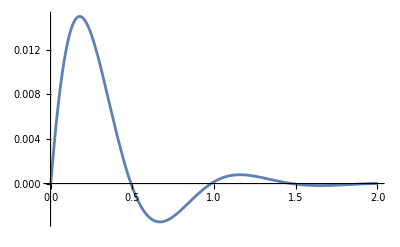

```mathematica
Clear["Global`*"]

Vin[t_] = Piecewise[{{0.6 *SquareWave[t], t<0.003}, {0, t>0.003}}]
eqn = v''[t] + 6v'[t] + 50v[t] == 100 Vin[t]; 
Vo = NDSolve[{eqn,v[0]==0, v'[0] == 0},v,{t,0,2,0.001 }]
Plot[Evaluate[v[t] /. Vo],{t,0,2}, PlotRange->All]
```

#### Response to square wave

0.6 SquareWave[t]

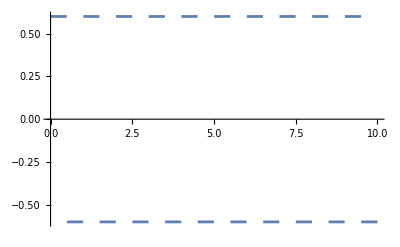

50 b[t]+6 b'[t]+b''[t]==60. SquareWave[t]

{{b→InterpolatingFunction[…]}}

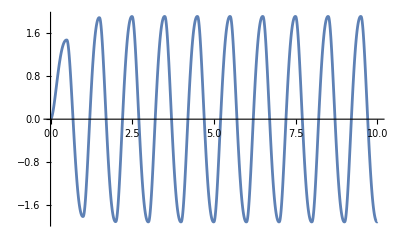

```mathematica
Vin2[t_] = 0.6 SquareWave[t] 
Plot[Vin2[t], {t,0,10}]
eqn2 = b''[t] + 6b'[t] + 50b[t] == 100 Vin2[t]
Vo2 = NDSolve[{eqn2,b[0]==0,b'[0] == 0},b,{t,0,10,0.1 }]
Plot[Evaluate[b[t] /. Vo2],{t,0,10}]
```

#### Arbitrary input

Piecewise[{{(-1+t)^2, 0<t<1}, {Log[t], t≥1}, {0, True}}]

-Graphics-

{{v→InterpolatingFunction[…]}}

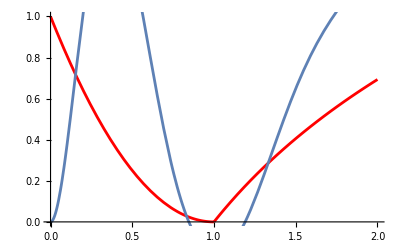

```mathematica
Vin[t_] = Piecewise[{{(t-1)^2,0<t<1  } , {Log[t],t>=1}}]
pltin = Plot[Vin[t],{t,0,2}, PlotStyle->Red]
eqn = v''[t] + 6v'[t] + 50v[t] == 100 Vin[t]; 
Vo = NDSolve[{eqn,v[0]==0, v'[0] == 0},v,{t,0,2,0.001 }]
plto = Plot[Evaluate[v[t] /. Vo],{t,0,2}, PlotRange->All];
Show[{pltin, plto}]
```

## Comments

I am curious on why the outputs are the way they are. I still don’t get the intuition behind the Impulse Response & Transfer Function. This Assignment motivates me to look into more in depth explanation of digital signals.